```mathematica
(* Requires shell-thermal2.nb *)
densityTable=(BoltzTable/.kT->50/nKPerHz);
```

```mathematica
densityTableT[temp_]:=(BoltzTable/.kT->temp/nKPerHz);
```

```mathematica
Δ1
```

3.53303×10^6

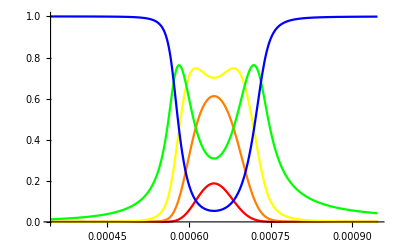

```mathematica
evectors[x_,y_,z_]:=AdiabaticVectorsChipC[(*Δ1*)3.51*^6,Ωc*XCosineAccurateC2[x,y,z]*MagFracC2[x,y,z],x,y,z][[1]]; (* select only the e-vector which approaches |2,2> adiabatically when the rf is turned off. *)
Show@(MapThread[Plot[evectors[x1,y1,z][[#1]],{z,z1-0.3*10^-3,z1+0.3*10^-3},PlotRange->All,PlotStyle->#2]&,{Range[5],{Red,Orange,Yellow,Green,Blue}}])
```

```mathematica
(* DOUBLE-CHECK WHICH IS WHICH *)
```

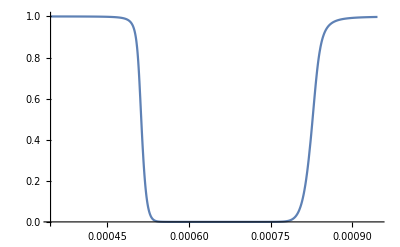

```mathematica
Plot[evectors[x1,y1,z][[5]],{z,z1-0.3*10^-3,z1+0.3*10^-3},PlotRange->All]
```

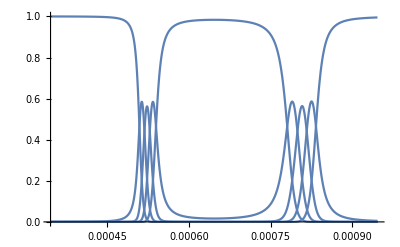

```mathematica
Plot[Abs[#]^2&/@evectors[x1,y1,z],{z,z1-0.3*10^-3,z1+0.3*10^-3},PlotRange->All]
```

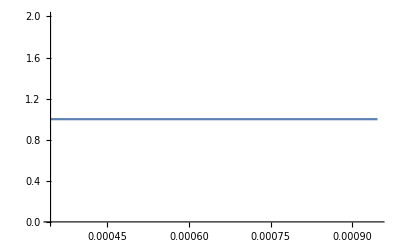

```mathematica
Plot[Total[Abs[#]^2&/@evectors[x1,y1,z]],{z,z1-0.3*10^-3,z1+0.3*10^-3},PlotRange->All]
```

```mathematica
evectorsn2[x_,y_,z_]:=evectors[x,y,z][[1]];
evectorsn1[x_,y_,z_]:=evectors[x,y,z][[2]];
evectors0[x_,y_,z_]:=evectors[x,y,z][[3]];
evectors1[x_,y_,z_]:=evectors[x,y,z][[4]];
evectors2[x_,y_,z_]:=evectors[x,y,z][[5]];
```

```mathematica
evectorn2Table=(Parallelize@Table[evectorsn2[x mm,y mm,z mm],
{z,z1/mm-aBox/mm/2,z1/mm+aBox/mm/2,BoltzPixel/mm},{y,y1/mm-aBox/mm/2,y1/mm+aBox/mm/2,BoltzPixel/mm},{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm}]);
```

```mathematica
evectorn1Table=(Parallelize@Table[evectorsn1[x mm,y mm,z mm],
{z,z1/mm-aBox/mm/2,z1/mm+aBox/mm/2,BoltzPixel/mm},{y,y1/mm-aBox/mm/2,y1/mm+aBox/mm/2,BoltzPixel/mm},{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm}]);
```

```mathematica
evector0Table=(Parallelize@Table[evectors0[x mm,y mm,z mm],
{z,z1/mm-aBox/mm/2,z1/mm+aBox/mm/2,BoltzPixel/mm},{y,y1/mm-aBox/mm/2,y1/mm+aBox/mm/2,BoltzPixel/mm},{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm}]);
```

```mathematica
evector1Table=(Parallelize@Table[evectors1[x mm,y mm,z mm],
{z,z1/mm-aBox/mm/2,z1/mm+aBox/mm/2,BoltzPixel/mm},{y,y1/mm-aBox/mm/2,y1/mm+aBox/mm/2,BoltzPixel/mm},{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm}]);
```

```mathematica
evector2Table=(Parallelize@Table[evectors2[x mm,y mm,z mm],
{z,z1/mm-aBox/mm/2,z1/mm+aBox/mm/2,BoltzPixel/mm},{y,y1/mm-aBox/mm/2,y1/mm+aBox/mm/2,BoltzPixel/mm},{x,x1/mm-aBox/mm,x1/mm+aBox/mm,BoltzPixel/mm}]);
```

```mathematica
sqrdTables=(Abs[#]^2&/@{evectorn2Table,evectorn1Table,evector0Table,evector1Table,evector2Table});
```

```mathematica
stateLabels={-2,-1,0,1,2};
```

```mathematica
ListPlot[(Total@sqrdTables[[All,50,50,#]])&/@Range[1,Dimensions[evector0Table][[3]]]]
```

```mathematica
popTables[temp_]:=(densityTableT[temp]*#&/@sqrdTables);
```

```mathematica
ArrayPlot[Total[popTables[50][[1]],{2}],ColorFunction->"Thermometer"]
```

```mathematica
ArrayPlot[Total[popTables[50][[3]],{2}],ColorFunction->"Thermometer"]
```

```mathematica
ArrayPlot[Total[popTables[50][[5]],{2}],ColorFunction->"Thermometer"]
```

```mathematica
ListPlot[Total[#,{2,3}]&/@popTables[50]]
```

```mathematica
temps={25,50,100,200,320};
```

```mathematica
relSpinPopVTemps=((Total[#,3]&/@popTables[#])/Total[densityTableT[#],3])&/@{25,50,100,200,320};
ListLinePlot[relSpinPopVTemps]
```

```mathematica
Dimensions@relSpinPopVTemps
```

```mathematica
Total@relSpinPopVTemps[[1]]
```

```mathematica
ListLinePlot[
MapThread[{#1,#2}&,{stateLabels,#}]&/@relSpinPopVTemps,
PlotLegends->temps,
Ticks->{{-2,-1,0,1,2},Automatic},
PlotLabel->"Rel. population in each atomic spin state for different temps."
]
```

```mathematica
ListLinePlot[
MapThread[{#1,#2}&,{temps,relSpinPopVTemps[[All,#]]}]&/@Range[5],
PlotLegends->stateLabels,
PlotLabel->"Rel. spin populations as a function of temp.",
AxesLabel->{"temp [K]","rel. spin pop."}
]
```

```mathematica
ListLinePlot[
MapThread[{#1,(#[[3]]/(#[[1]]+#[[5]]))&[#2]}&,{temps,relSpinPopVTemps}],
AxesLabel->{"temp [K]","ratio"},
PlotLabel->{"pop0/(pop2 + pop-2"}
]
```